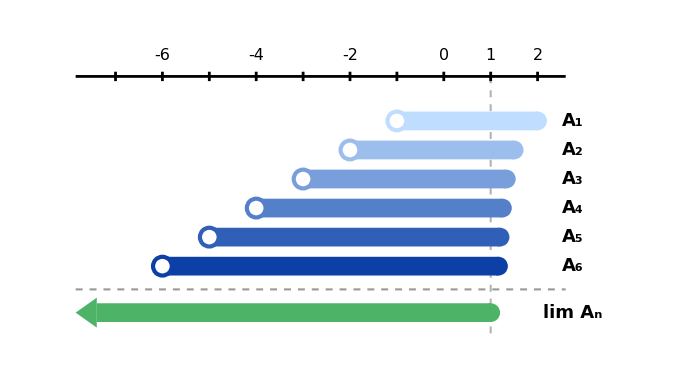

CloudObject[https://www.wolframcloud.com/obj/jesusparejop/Parcial26-27_1.png]

```mathematica
ClearAll[h, sep, nMax, xIzq, yEje, yUlt, ySep, yLim, colorA, colorLim, abierto, cerrado,
  barra, filaA, ejeReal, guia, separador, limite, diagrama1];

h = 0.2;       (* radio de los puntos = semialtura de las barras *)
sep = 0.62;    (* separación vertical entre filas *)
nMax = 6;
xIzq = -7.4;
yEje = 0.95;

colorA[n_] := Blend[{RGBColor[0.75, 0.87, 1], RGBColor[0.05, 0.25, 0.65]}, (n - 1)/(nMax - 1)];
colorLim = RGBColor[0.3, 0.7, 0.4];

abierto[x_, y_, col_] := {White, Disk[{x, y}, h], col, AbsoluteThickness[3], Circle[{x, y}, h]};
cerrado[x_, y_, col_] := {col, Disk[{x, y}, h]};
barra[l_, r_, y_, col_] := {col, Rectangle[{l, y - h}, {r, y + h}]};

(* A_n = (-n, 1+1/n] *)
filaA[n_] := Module[{y = -(n - 1) sep, col = colorA[n]},
   {barra[-n, 1 + 1/n, y, col], abierto[-n, y, col], cerrado[1 + 1/n, y, col],
    Text[Style[Subscript["A", n], 18, Bold], {2.75, y}, {-1, 0}]}];

yUlt = -(nMax - 1) sep;
ySep = yUlt - 0.8 sep;
yLim = yUlt - 1.6 sep;

ejeReal = {Black, AbsoluteThickness[2], Line[{{xIzq - 0.45, yEje}, {2.6, yEje}}],
   Table[Line[{{k, yEje - 0.1}, {k, yEje + 0.1}}], {k, -7, 2}],
   Table[Text[Style[k, 16], {k, yEje + 0.45}], {k, {-6, -4, -2, 0, 1, 2}}]};

guia = {GrayLevel[0.7], Dashed, AbsoluteThickness[1.5], Line[{{1, yEje}, {1, yLim - 0.45}}]};
separador = {GrayLevel[0.6], Dashed, AbsoluteThickness[1.5],
   Line[{{xIzq - 0.45, ySep}, {2.6, ySep}}]};

(* límite: semirrecta (-inf, 1] *)
limite = {
   barra[xIzq, 1, yLim, colorLim],
   {colorLim, Polygon[{{xIzq, yLim + 1.6 h}, {xIzq, yLim - 1.6 h}, {xIzq - 0.45, yLim}}]},
   cerrado[1, yLim, colorLim],
   Text[Style[Row[{"lim ", Subscript["A", "n"]}], 18, Bold], {2.75, yLim}, {-1, 0}]};

diagrama1 = Graphics[
   {guia, ejeReal, Table[filaA[n], {n, 1, nMax}], separador, limite},
   PlotRange -> {{xIzq - 0.7, 4.1}, {yLim - 0.6, yEje + 0.9}}, ImageSize -> 700];

diagrama1

Export[CloudObject["Parcial26-27_1.png"], diagrama1, "PNG", Background -> None, ImageResolution -> 300, ImageSize -> 700]
```

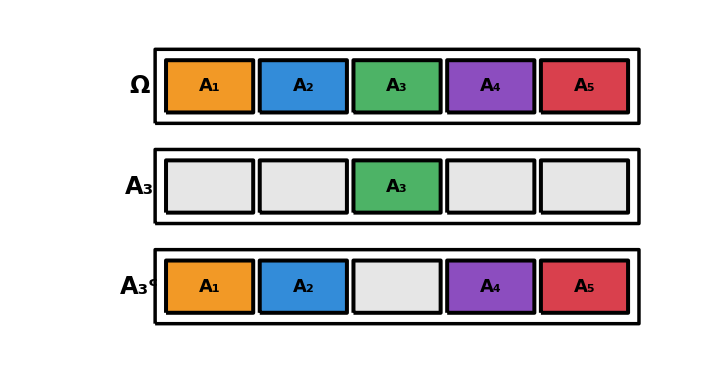

CloudObject[https://www.wolframcloud.com/obj/jesusparejop/Parcial26-27_2.png]

```mathematica
ClearAll[nB, iSel, colB, gris, ancho, gap, xIni, bloque, fila, marco, y1, y2, y3, diagrama2];

nB = 5; iSel = 3;
colB = {RGBColor[0.95, 0.6, 0.15], RGBColor[0.2, 0.55, 0.85], RGBColor[0.3, 0.7, 0.4],
   RGBColor[0.55, 0.3, 0.75], RGBColor[0.85, 0.25, 0.3]};
gris = GrayLevel[0.9];
ancho = 2; gap = 0.15;

xIni[k_] := (k - 1) (ancho + gap);

bloque[k_, y_, activo_, etiqueta_] := {
   If[activo, colB[[k]], gris], EdgeForm[{Black, Thickness[0.004]}],
   Rectangle[{xIni[k], y}, {xIni[k] + ancho, y + 1.2}, RoundingRadius -> 0.1],
   If[etiqueta, {Black, Text[Style[Subscript["A", k], 18, Bold], {xIni[k] + ancho/2, y + 0.6}]}, {}]};

fila[y_, activos_List, etiquetados_List] :=
  Table[bloque[k, y, MemberQ[activos, k], MemberQ[etiquetados, k]], {k, 1, nB}];

marco[y_] := {FaceForm[None], EdgeForm[{Black, AbsoluteThickness[2.5]}],
   Rectangle[{-0.25, y - 0.25}, {xIni[nB] + ancho + 0.25, y + 1.45}, RoundingRadius -> 0.2]};

y1 = 0; y2 = -2.3; y3 = -4.6;

diagrama2 = Graphics[{
    marco[y1], fila[y1, Range[nB], Range[nB]],
    marco[y2], fila[y2, {iSel}, {iSel}],
    marco[y3], fila[y3, Complement[Range[nB], {iSel}], Complement[Range[nB], {iSel}]],
    {Black, Text[Style["Ω", 24, Bold], {-0.6, y1 + 0.6}, {1, 0}]},
    {Black, Text[Style[Subscript["A", iSel], 24, Bold], {-0.6, y2 + 0.6}, {1, 0}]},
    {Black, Text[Style[Subsuperscript["A", iSel, "c"], 24, Bold], {-0.6, y3 + 0.6}, {1, 0}]}},
   PlotRange -> {{-2.3, xIni[nB] + ancho + 0.6}, {y3 - 0.6, y1 + 1.8}}, ImageSize -> 720];

diagrama2

Export[CloudObject["Parcial26-27_2.png"], diagrama2, "PNG", Background -> None, ImageResolution -> 300, ImageSize -> 720]
```

```mathematica
ClearAll[nCuadros, colE, gris, cuadro, etiquetaE, medidaCero, llave, panel, colG, colR,
  lineaFinita, lineaNumerable, diagrama3];

nCuadros = 7;
colE = {RGBColor[0.95, 0.6, 0.15], RGBColor[0.2, 0.55, 0.85], RGBColor[0.3, 0.7, 0.4],
   RGBColor[0.55, 0.3, 0.75], RGBColor[0.85, 0.25, 0.3], RGBColor[0.85, 0.75, 0.15],
   RGBColor[0.2, 0.7, 0.7]};
gris = GrayLevel[0.9];
colG = RGBColor[0.2, 0.6, 0.3];
colR = RGBColor[0.8, 0.15, 0.2];

(* cada cuadro es un elemento de N, es decir, un conjunto unipuntual E_k *)
cuadro[k_, activo_] := {
   If[activo, colE[[k]], gris], EdgeForm[{Black, Thickness[0.004]}],
   Rectangle[{k - 0.42, -0.42}, {k + 0.42, 0.42}, RoundingRadius -> 0.1],
   Text[Style[k, 18, Bold, If[activo, Black, GrayLevel[0.5]]], {k, 0}]};

etiquetaE[k_] := Text[Style[Subscript["E", k], 15, Bold, Black], {k, -0.8}];
medidaCero[k_] := Text[Style["0", 16, GrayLevel[0.3]], {k, 0.8}];

llave[xa_, xb_, y_, col_] := {col, AbsoluteThickness[3],
   Line[{{xa, y}, {xa, y - 0.22}, {(xa + xb)/2 - 0.3, y - 0.22}, {(xa + xb)/2, y - 0.5},
     {(xa + xb)/2 + 0.3, y - 0.22}, {xb, y - 0.22}, {xb, y}}]};

panel[nAct_, colLlave_, xFin_] := Graphics[{
    Table[cuadro[k, k ≤ nAct], {k, 1, nCuadros}],
    Table[{etiquetaE[k], medidaCero[k]}, {k, 1, nAct}],
    Text[Style["μ", 18, Bold, Black], {0.1, 0.8}, {1, 0}],
    Text[Style["…", 28, Bold, Black], {nCuadros + 1, 0}],
    llave[0.55, xFin, -1.2, colLlave]},
   PlotRange -> {{-0.6, nCuadros + 1.7}, {-1.9, 1.3}}, ImageSize -> 520];

lineaFinita = Row[{Style["suma: 0", 18], Spacer[30], Style["unión: 0", 18], Spacer[30],
    Style["=", 30, Bold, colG]}];
lineaNumerable = Row[{Style["suma: 0", 18], Spacer[30],
    Style["unión: ∞", 18, Bold, colR], Spacer[30],
    Style["≠", 30, Bold, colR]}];

diagrama3 = Column[{
    Style["Unión finita", 22, Bold], panel[3, colG, 3.45], lineaFinita,
    Spacer[25],
    Style["Unión numerable", 22, Bold], panel[7, colR, 8.45], lineaNumerable},
   Alignment -> Center, Spacings -> 0.7];

diagrama3

Export[CloudObject["Parcial26-27_3.png"], diagrama3, "PNG", Background -> None, ImageResolution -> 300, ImageSize -> 600]
```

Unión finita
-Graphics-
suma: 0unión: 0=

Unión numerable
-Graphics-
suma: 0unión: ∞≠

CloudObject[https://www.wolframcloud.com/obj/jesusparejop/Parcial26-27_3.png]

```mathematica
ClearAll[x, y];
ClearAll[inA1, inA2, inA3, c1, c2, c3, regionPlano, panelA, panelC, panelD, flecha,
  colA, colC, colD, diagrama4];

inA1 = (x + 1)^2 + (y - 0.2)^2 < 1.44;
inA2 = (x - 0.1)^2 + (y + 0.35)^2 < 1.44;
inA3 = (x - 1)^2 + (y - 0.3)^2 < 1.44;

c1 = RGBColor[0.2, 0.55, 0.85];
c2 = RGBColor[0.95, 0.6, 0.15];
c3 = RGBColor[0.3, 0.7, 0.4];

regionPlano[cond_, estilo_, borde_] := RegionPlot[cond, {x, -2.5, 2.5}, {y, -1.9, 2.1},
   PlotStyle -> estilo, BoundaryStyle -> borde, PlotPoints -> 60, MaxRecursion -> 3];

(* Panel 1: la sucesión A_n, con solapamientos *)
panelA = Show[
   regionPlano[inA1, Directive[c1, Opacity[0.45]], None],
   regionPlano[inA2, Directive[c2, Opacity[0.45]], None],
   regionPlano[inA3, Directive[c3, Opacity[0.45]], None],
   Graphics[{Black, AbsoluteThickness[2],
     Circle[{-1, 0.2}, 1.2], Circle[{0.1, -0.35}, 1.2], Circle[{1, 0.3}, 1.2],
     Text[Style["A₁", 20, Bold], {-1.5, 0.3}],
     Text[Style["A₂", 20, Bold], {0.2, -1.05}],
     Text[Style["A₃", 20, Bold], {1.7, 0.7}]}],
   PlotRange -> {{-2.5, 2.5}, {-1.9, 2.1}}, PlotRangePadding -> None,
   Frame -> False, Axes -> False, AspectRatio -> Automatic, ImageSize -> 250];

(* Panel 2: las uniones acumuladas C_n, cada vez más grandes *)
panelC = Show[
   regionPlano[inA1 || inA2 || inA3, RGBColor[0.82, 0.9, 0.99], Directive[Black, AbsoluteThickness[1.5]]],
   regionPlano[inA1 || inA2, RGBColor[0.55, 0.72, 0.95], Directive[Black, AbsoluteThickness[1.5]]],
   regionPlano[inA1, RGBColor[0.2, 0.4, 0.8], Directive[Black, AbsoluteThickness[1.5]]],
   Graphics[{
     Text[Style["C₁", 20, Bold, White], {-1.5, 0.3}],
     Text[Style["C₂", 20, Bold, Black], {0.3, -0.8}],
     Text[Style["C₃", 20, Bold, Black], {1.7, 0.7}]}],
   PlotRange -> {{-2.5, 2.5}, {-1.9, 2.1}}, PlotRangePadding -> None,
   Frame -> False, Axes -> False, AspectRatio -> Automatic, ImageSize -> 250];

(* Panel 3: los trozos disjuntos D_n = C_n \ C_(n-1) *)
panelD = Show[
   regionPlano[inA1, Directive[c1, Opacity[0.85]], Directive[Black, AbsoluteThickness[1.5]]],
   regionPlano[inA2 && ! inA1, Directive[c2, Opacity[0.85]], Directive[Black, AbsoluteThickness[1.5]]],
   regionPlano[inA3 && ! (inA1 || inA2), Directive[c3, Opacity[0.85]], Directive[Black, AbsoluteThickness[1.5]]],
   Graphics[{
     Text[Style["D₁", 20, Bold, Black], {-1.5, 0.3}],
     Text[Style["D₂", 20, Bold, Black], {0.3, -0.8}],
     Text[Style["D₃", 20, Bold, Black], {1.7, 0.7}]}],
   PlotRange -> {{-2.5, 2.5}, {-1.9, 2.1}}, PlotRangePadding -> None,
   Frame -> False, Axes -> False, AspectRatio -> Automatic, ImageSize -> 250];

flecha = Graphics[{Black, AbsoluteThickness[3], Arrowheads[0.25], Arrow[{{0, 0}, {1, 0}}]},
   ImageSize -> {55, 30}, PlotRange -> {{-0.1, 1.1}, {-0.3, 0.3}}];

colA = Column[{Style["Aₙ", 24, Bold], panelA}, Alignment -> Center, Spacings -> 0.4];
colC = Column[{Style["Cₙ", 24, Bold], panelC}, Alignment -> Center, Spacings -> 0.4];
colD = Column[{Style["Dₙ", 24, Bold], panelD}, Alignment -> Center, Spacings -> 0.4];

diagrama4 = Grid[{{colA, flecha, colC, flecha, colD}},
   Alignment -> Center, Spacings -> {1, 0}];

diagrama4

Export[CloudObject["Parcial26-27_4.png"], diagrama4, "PNG", Background -> None, ImageResolution -> 300, ImageSize -> 900]
```

Aₙ
-Graphics- | -Graphics- | Cₙ
-Graphics- | -Graphics- | Dₙ
-Graphics-

CloudObject[https://www.wolframcloud.com/obj/jesusparejop/Parcial26-27_4.png]